```mathematica
NS["fmri_alzheimer_testconsistency.nb"]
```

```mathematica
(* Load data given by Claudia *)
(*relevant={7,3,27,28,2,10,16,22,4,12,18,24};*)
(*relevant=Range[28];*)
(* relevant quantities found in fmri_alzheimer_reduction170317.nb *)
relevant={1,2,3,8,9,12};
datah=Import["claudia_RGS_graphprop22_Con.txt","CSV"];
datah=datah[[relevant,2;;]];

smean=Mean[T@datah];snorm=1/Std[T@datah];
datah=N[snorm*(datah-smean)];

dataa=Import["claudia_RGS_graphprop22_AD.txt","CSV"];
quantities=T[dataa][[1]][[relevant]];
dataa=dataa[[relevant,2;;]];
dataa=N[snorm*(dataa-smean)];

datam=Import["claudia_RGS_graphprop22_MCI.txt","CSV"];
datam=datam[[relevant,2;;]];
datam=N[snorm*(datam-smean)];

nq=Length[quantities];
health={1,2,3};
data[1]=datah;data[2]=dataa;data[3]=datam;
```

```mathematica
ClearAll[nindiv,means,dscatter,idscatter,scalematrix,param];
Do[nindiv[i]=Length[T[data[i]]];
means[i]=Mean@T@data[i];
dscatter[i]=(nindiv[i]+1)/nindiv[i]*(data[i]-means[i]).T[data[i]-means[i]]; 
idscatter[i]=Inverse[dscatter[i]];
scalematrix[i]=dscatter[i]/(nindiv[i]+1-nq);
param[i]=nindiv[i]+1-nq;
,{i,health}];
```

```mathematica
lnpdf[i_,x_]:=Log[Gamma[(nindiv[i]+1)/2]]-Log[Gamma[(nindiv[i]+1-nq)/2]]-Log[Det[dscatter[i]*Pi]]/2-(nindiv[i]+1)*Log[1+(x-means[i]).idscatter[i].(x-means[i])]/2;
```

```mathematica
plevel[i_,p_]:=InverseCDF[FRatioDistribution[nq,nindiv[i]+1-nq],p]
```

```mathematica
lnmtd[i_,x_]:=Log@PDF[MultivariateTDistribution[means[i],scalematrix[i],param[i]],x]
```

```mathematica
ii=2
```

2

```mathematica
lev=plevel[ii,0.95]
```

3.37375

```mathematica
NProbability[({x1,x2,x3,x4,x5,x6}-means[ii]).Inverse[scalematrix[ii]].({x1,x2,x3,x4,x5,x6}-means[ii])<lev*nq,{x1,x2,x3,x4,x5,x6}\[Distributed]MultivariateTDistribution[means[ii],scalematrix[ii],param[ii]], PrecisionGoal->2,AccuracyGoal->Infinity]
```

0.950492

```mathematica
NProbability[({x1,x2,x3,x4,x5}-means[1]).idscatter[1].({x1,x2,x3,x4,x5}-means[1])<lev,{x1,x2,x3,x4,x5}\[Distributed]MultivariateTDistribution[means[1],scalematrix[1],param[1]], PrecisionGoal->2,AccuracyGoal->Infinity]
```

1.0009

```mathematica
xx=RandomReal[{-50,50},4];{lnmtd[3,xx],lnpdf[3,xx]}
```

{-78.7607,-78.7607}

```mathematica
lnpdf[1,
```

```mathematica
Sort@quantities
```

{closeness centrality3,cluster coeff1.,cluster coeff.4,graphweights1,graphweights2,graphweights3,graphweights4,modularity,shortest path1,shortest path3,weighted degree2,weighted degree4}

```mathematica
Dimensions/@{datah,dataa,datam}
```

{{12,26},{12,14},{12,16}}

```mathematica
Table[{i,quantities[[i]]},{i,nq}]//MF
```

(1 | graphweights1
2 | shortest path1
3 | cluster coeff1.
4 | modularity
5 | graphweights2
6 | weighted degree2
7 | graphweights3
8 | shortest path3
9 | closeness centrality3
10 | graphweights4
11 | cluster coeff.4
12 | weighted degree4)

```mathematica
plevel[2,0.95]
```

8.74464

```mathematica
prob[x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_,x11_,x12_]=Simplify[Exp@lnpdf[1,{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12}]]
```

0.31655/(1.+7.02006 x1^2+4.03801 x10^2-3.27476×10^-16 x11+0.573175 x11^2+3.71236×10^-16 x12-0.490078 x11 x12+0.953733 x12^2-3.14697×10^-15 x2+0.276411 x11 x2-0.937311 x12 x2+2.02297 x2^2-6.36102×10^-15 x3+0.245751 x11 x3-0.168712 x12 x3+2.03626 x2 x3+3.91071 x3^2+1.06808×10^-16 x4-0.146814 x11 x4+0.236172 x12 x4-0.265216 x2 x4-0.133927 x3 x4+0.133484 x4^2-5.33807×10^-15 x5-1.0476 x11 x5-0.0151434 x12 x5+3.37423 x2 x5+5.70222 x3 x5+0.122573 x4 x5+3.86633 x5^2+1.11081×10^-15 x6-1.03935 x11 x6-0.131891 x12 x6-0.536076 x2 x6-1.26377 x3 x6+0.293752 x4 x6+0.279346 x5 x6+1.14392 x6^2-2.72017×10^-15 x7+1.16499 x11 x7-2.17398 x12 x7+3.58917 x2 x7+2.08438 x3 x7-0.572238 x4 x7+1.93814 x5 x7-1.64935 x6 x7+2.80481 x7^2+1.01606×10^-15 x8-0.0824352 x11 x8+0.216549 x12 x8-1.14552 x2 x8-0.72968 x3 x8+0.136955 x4 x8-0.958822 x5 x8+0.258264 x6 x8-0.936418 x7 x8+0.232002 x8^2+x10 (4.47529×10^-15-0.337212 x11+1.01068 x12-4.95542 x2-3.54263 x3+0.0312139 x4-5.43521 x5+0.418423 x6-4.75318 x7+1.14248 x8+0.438663 x9)+7.66743×10^-16 x9-0.106338 x11 x9+0.0729442 x12 x9-0.12714 x2 x9-1.02486 x3 x9-0.0205611 x4 x9-0.633066 x5 x9+0.00581104 x6 x9-0.174757 x7 x9+0.0367318 x8 x9+0.148708 x9^2+x1 (5.41209×10^-15-0.920842 x10+0.777264 x11-0.706195 x12+1.06965 x2-8.45769 x3+0.0713475 x4-5.60813 x5+0.637638 x6+1.31867 x7+0.105305 x8+1.08183 x9))^(27/2)

```mathematica
prob[500,0,0,0,0,0,0,0,0,0,0,0]
```

1.5946×10^-85

```mathematica
lev=plevel[1,0.0005]
```

0.129231

```mathematica
lev=1000
```

1000

```mathematica
rang[x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_,x11_,x12_]=Simplify@(({x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12}-means[1]).idscatter[1].({x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12}-means[1])<lev)
```

1. x1^2+0.57521 x10^2+0.0816482 x11^2+5.28822×10^-17 x12+0.135858 x12^2+0.0393744 x11 x2+0.28817 x2^2+0.035007 x11 x3+0.290063 x2 x3+0.557076 x3^2+1.52147×10^-17 x4+0.0336424 x12 x4+0.0190147 x4^2+0.480656 x2 x5+0.812276 x3 x5+0.0174604 x4 x5+0.550755 x5^2+1.58234×10^-16 x6+0.0418447 x4 x6+0.0397926 x5 x6+0.16295 x6^2+0.165952 x11 x7+0.511273 x2 x7+0.296918 x3 x7+0.276086 x5 x7+0.399542 x7^2+1.44736×10^-16 x8+0.0308472 x12 x8+0.0195091 x4 x8+0.0367895 x6 x8+0.0330485 x8^2+x10 (6.37501×10^-16-0.0480355 x11+0.14397 x12-0.705895 x2-0.504644 x3+0.00444639 x4-0.77424 x5+0.0596039 x6-0.677086 x7+0.162745 x8+0.0624872 x9)+x1 (7.70947×10^-16-0.131173 x10+0.11072 x11-0.100597 x12+0.152371 x2-1.20479 x3+0.0101634 x4-0.798872 x5+0.0908309 x6+0.187843 x7+0.0150006 x8+0.154106 x9)+1.09222×10^-16 x9+0.0103908 x12 x9+0.000827777 x6 x9+0.00523241 x8 x9+0.0211833 x9^2<142.449+4.66486×10^-17 x11+0.0698111 x11 x12+4.48283×10^-16 x2+0.133519 x12 x2+9.0612×10^-16 x3+0.0240328 x12 x3+0.0209135 x11 x4+0.0377797 x2 x4+0.0190778 x3 x4+7.60403×10^-16 x5+0.149229 x11 x5+0.00215716 x12 x5+0.148054 x11 x6+0.0187878 x12 x6+0.0763634 x2 x6+0.180023 x3 x6+3.87486×10^-16 x7+0.309681 x12 x7+0.0815148 x4 x7+0.234949 x6 x7+0.0117428 x11 x8+0.163178 x2 x8+0.103942 x3 x8+0.136583 x5 x8+0.133392 x7 x8+0.0151478 x11 x9+0.0181109 x2 x9+0.14599 x3 x9+0.0029289 x4 x9+0.0901797 x5 x9+0.024894 x7 x9

```mathematica
rang[0,0,0,0,0,0,0,0,0,0,0,0]
```

True

```mathematica
Sqrt@Eigensystem[dscatter[1]][[1]]
```

{13.2059,8.8186,5.33598,4.18272,3.5827,2.61003,1.74119,1.31694,0.945713,0.608342,0.338568,0.276693}

```mathematica
NIntegrate[prob[x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12](*Boole[rang[x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12]]*),{x1,-50,50},{x2,-50,50},{x3,-50,50},{x4,-50,50},{x5,-50,50},{x6,-50,50},{x7,-50,50},{x8,-50,50},{x9,-50,50},{x10,-50,50},{x11,-50,50},{x12,-50,50},PrecisionGoal->1,AccuracyGoal->+Infinity]
```

$Aborted

```mathematica
Install["Cuba\\Cuhre"];Install["Cuba\\Suave"];Install["Cuba\\Vegas"];Install["Cuba\\Divonne"];
```

```mathematica
Vegas[prob[x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12](*Boole[rang[x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12]]*),{x1,-50,50},{x2,-50,50},{x3,-50,50},{x4,-50,50},{x5,-50,50},{x6,-50,50},{x7,-50,50},{x8,-50,50},{x9,-50,50},{x10,-50,50},{x11,-50,50},{x12,-50,50},MaxPoints->2*10^6,PrecisionGoal->3,AccuracyGoal->+Infinity]
```

$Aborted

```mathematica
Do[es=Eigensystem[istdmatrix[i]];eva[i]=es[[1]];eve[i]=Last[es[[2]]];,{i,3}]
```

```mathematica
Table[eva[i],{i,3}]//MF
```

(169.804 | 113.41 | 35.1275 | 14.5353 | 7.4957 | 4.28796 | 1.90832 | 1.0128 | 0.743062 | 0.456579 | 0.167165 | 0.0745435
187432. | 667.899 | 239.912 | 105.41 | 70.2017 | 15.6604 | 5.11172 | 1.0176 | 0.186225 | 0.0413948 | 0.0223546 | 0.000256191
24897. | 1615.05 | 75.7674 | 43.5713 | 16.1311 | 9.26459 | 3.78413 | 2.53918 | 0.892277 | 0.273173 | 0.0731261 | 0.0177012)

```mathematica
Table[eve[i],{i,3}]//T//MF
```

(-0.312441 | 0.0409846 | -0.285307
0.311488 | -0.0431976 | 0.237139
-0.313327 | 0.0570184 | -0.265483
0.104176 | -0.0403665 | 0.210954
-0.349476 | 0.0679612 | -0.389309
-0.308072 | 0.0228119 | -0.127876
-0.297887 | 0.0488924 | -0.364206
0.156784 | -0.0124005 | 0.0711597
-0.252746 | 0.564648 | -0.303863
-0.366046 | 0.0716328 | -0.583312
-0.314266 | 0.812346 | -0.092045
-0.263317 | 0.0049847 | -0.0264491)

```mathematica
xx=Array[x,nq]
```

{x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],x[11],x[12]}

```mathematica
region=FS[Norm[xx]<100]
```

√(Abs[x[1]]^2+Abs[x[2]]^2+Abs[x[3]]^2+Abs[x[4]]^2+Abs[x[5]]^2+Abs[x[6]]^2+Abs[x[7]]^2+Abs[x[8]]^2+Abs[x[9]]^2+Abs[x[10]]^2+Abs[x[11]]^2+Abs[x[12]]^2)<100

```mathematica
fun=FS@Sum[lnpdf[i,xx],{i,3}];
```

```mathematica
maxp=FindMaximum[{fun,region},xx]
```

{16.7611,{x[1]→-0.59086,x[2]→0.66996,x[3]→-0.55793,x[4]→0.435517,x[5]→-0.700426,x[6]→-0.402819,x[7]→-0.349592,x[8]→0.0903144,x[9]→-0.57563,x[10]→-0.538019,x[11]→-0.425067,x[12]→-0.230233}}

```mathematica
NMaximize[{fun,region},xx]
```

{16.7611,{x[1]→-0.591019,x[2]→0.670293,x[3]→-0.558093,x[4]→0.435883,x[5]→-0.700536,x[6]→-0.402883,x[7]→-0.349666,x[8]→0.0904953,x[9]→-0.575679,x[10]→-0.538082,x[11]→-0.425073,x[12]→-0.230245}}

```mathematica
maxpoint=(xx/.maxp[[2]])
```

{-0.59086,0.66996,-0.55793,0.435517,-0.700426,-0.402819,-0.349592,0.0903144,-0.57563,-0.538019,-0.425067,-0.230233}

```mathematica
region=FS[Norm[xx]<100]
```

√(Abs[x[1]]^2+Abs[x[2]]^2+Abs[x[3]]^2+Abs[x[4]]^2+Abs[x[5]]^2+Abs[x[6]]^2+Abs[x[7]]^2+Abs[x[8]]^2+Abs[x[9]]^2+Abs[x[10]]^2+Abs[x[11]]^2+Abs[x[12]]^2)<100

```mathematica
fun=FS@Sum[lnpdf[i,xx],{i,2}];
```

```mathematica
maxp=FindMaximum[{fun,region},xx]
```

{9.2122,{x[1]→-0.541207,x[2]→0.548849,x[3]→-0.498916,x[4]→0.333813,x[5]→-0.626627,x[6]→-0.291671,x[7]→-0.258092,x[8]→0.00476958,x[9]→-0.547147,x[10]→-0.474993,x[11]→-0.445558,x[12]→-0.214895}}

```mathematica
NMaximize[{fun,region},xx]
```

{9.2122,{x[1]→-0.541103,x[2]→0.548596,x[3]→-0.498804,x[4]→0.333301,x[5]→-0.626633,x[6]→-0.291697,x[7]→-0.258208,x[8]→0.00456721,x[9]→-0.547191,x[10]→-0.475056,x[11]→-0.445539,x[12]→-0.214905}}

```mathematica
maxpointah=(xx/.maxp[[2]])
```

{-0.541207,0.548849,-0.498916,0.333813,-0.626627,-0.291671,-0.258092,0.00476958,-0.547147,-0.474993,-0.445558,-0.214895}

```mathematica
fun=FS@Sum[lnpdf[i,xx],{i,{1,3}}];
```

```mathematica
maxp=FindMaximum[{fun,region},xx]
```

{6.7877,{x[1]→-0.346791,x[2]→0.363003,x[3]→-0.352931,x[4]→0.325477,x[5]→-0.421659,x[6]→-0.249764,x[7]→-0.178621,x[8]→0.0232986,x[9]→-0.521179,x[10]→-0.307931,x[11]→-0.365065,x[12]→-0.186661}}

```mathematica
NMaximize[{fun,region},xx]
```

{18.6267,{x[1]→-0.703256,x[2]→0.936076,x[3]→-0.674554,x[4]→0.446392,x[5]→-0.800587,x[6]→-0.461402,x[7]→-0.445247,x[8]→0.209379,x[9]→-0.622643,x[10]→-0.605959,x[11]→-0.432142,x[12]→-0.241086}}

```mathematica
maxpointmh=(xx/.maxp[[2]])
```

{-0.346791,0.363003,-0.352931,0.325477,-0.421659,-0.249764,-0.178621,0.0232986,-0.521179,-0.307931,-0.365065,-0.186661}

```mathematica
(* The three distributions are 6-dimensional. To visualize them, in this 6D space we choose a 2D section that passes through their centres. Then we plot the curves of 1 and 2 standard deviations. *)
point[1]=maxpointah;point[2]=maxpointmh;point[3]=maxpointam;

(* Affine-combination coefficients for the contour plot *)
ac[1,x_,y_]=-x-y/Sqrt[3]+1;ac[3,x_,y_]=x-y/Sqrt[3];ac[2,x_,y_]=Simplify[1-ac[1,x,y]-ac[3,x,y]];
seq=FS@Table[Sum[ac[ii,x,y]*point[ii][[jj]],{ii,3}],{jj,nq}]
```

{-0.541207-0.161928 x+0.317981 y,0.548849+0.38697 x-0.438014 y,-0.498916-0.175515 x+0.269902 y,0.333813+0.112081 x-0.0743355 y,-0.626627-0.173892 x+0.337073 y,-0.291671-0.169685 x+0.146358 y,-0.258092-0.187111 x+0.199794 y,0.00476958+0.204464 x-0.0966521 y,-0.547147-0.0754611 x+0.073553 y,-0.474993-0.130921 x+0.268494 y,-0.445558+0.0134095 x+0.0852034 y,-0.214895-0.0261823 x+0.0477191 y}

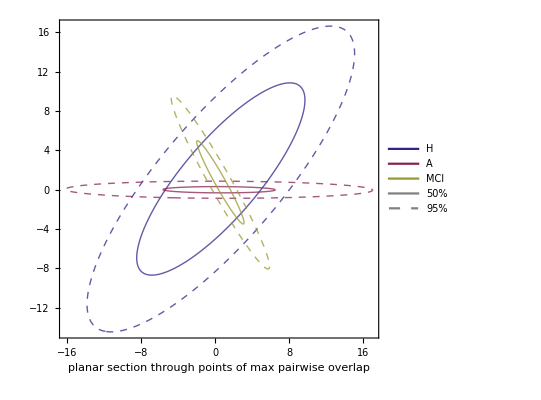

```mathematica
(* We plot the three separately and then join them *)
myfontsize=18;
colours={blue,red,yellow};Do[cont[i]=ContourPlot[(seq-means[i]).idscatter[i].(seq-means[i]),{x,-35,35},{y,-35,35},Contours->{plevel[i,0.5],plevel[i,0.95]},ContourShading->None,ContourStyle->{Directive[Opacity[0.75],Thick,colours[[i]]],Directive[Dashed,Opacity[0.75],Thick,colours[[i]]]},PlotPoints->300,FrameTicks->Auto,FrameLabel->Evaluate[myaxes[{"planar section through points of max pairwise overlap",""}]],PlotLegends->If[i==3,mylegendsc[{blue,red,yellow,White,{Gray,Thick},{Gray,Dashed,Thick}},{"H","A","MCI"," ", "50%","95%"}],None],(*PlotLabel->mylabels[{"1 and 2 standard deviations"}],*)PlotRange->All],{i,{1,3,2}}];
centres=Graphics[{{red,PointSize[Large],Point[{0,0}]}(*,{red,PointSize[Large],Point[{1/2,Sqrt[3]/2}]}*)(*,{yellow,PointSize[Large],Point[{1,0}]}*)}];

Show[Join[Array[cont,3](*,{centres}*)]]
```

```mathematica
expdf["std95_12_params_pairwiseoverlaps"]
```

../work/std95_12_params_pairwiseoverlaps.pdf

```mathematica
MaxH={{-22,22},{-6,6}};
AaxH={{-22,22},{-1.5,1.5}};

HaxA={{-20,20},{-30,30}};
MaxA={{-80,80},{-4,4}};

HaxM={{-15,15},{-26,26}};
AaxM={{-16,16},{-26,26}};
```

```mathematica
(* The three distributions are 6-dimensional. To visualize them, in this 6D space we choose a 2D section that passes through their centres. Then we plot the curves of 1 and 2 standard deviations. *)
point[1]=maxpointah;point[2]=maxpointmh;point[3]=maxpointam;
point[1]=means[1];point[2]=means[2];point[3]=means[3];

(* Affine-combination coefficients for the contour plot *)
ac[1,x_,y_]=-x-y/Sqrt[3]+1;ac[3,x_,y_]=x-y/Sqrt[3];ac[2,x_,y_]=Simplify[1-ac[1,x,y]-ac[3,x,y]];
seqf[x_,y_]=FS@Table[Sum[ac[ii,x,y]*point[ii][[jj]],{ii,3}],{jj,nq}]
```

{-4.27009×10^-17-0.30036 x-0.517448 y,6.93889×10^-16+0.422756 x+0.921967 y,7.62211×10^-16-0.31284 x-0.391014 y,6.12758×10^-16+0.493798 x+0.247622 y,-1.57993×10^-16-0.278029 x-0.369567 y,-4.27009×10^-18-0.25148 x-0.154525 y,-9.39419×10^-17+0.0245361 x-0.139253 y,-7.25915×10^-17+0.0698809 x+0.367994 y,1.06752×10^-16-0.379939 x+2.51088 y,4.27009×10^-17-0.00032102 x-0.242388 y,2.77556×10^-17-0.322087 x+3.92 y,2.13504×10^-18-0.191212 x-0.122483 y}

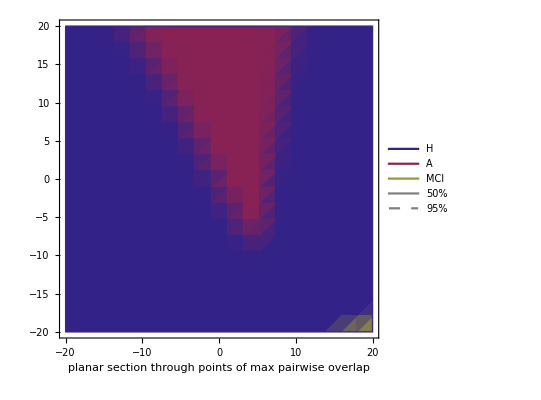

```mathematica
myfontsize=18;
colours={blue,red,yellow};RegionPlot[True,{x,-20,20},{y,-20,20},ColorFunction->Function[{x,y},Blend[{blue,red,yellow},{Exp@lnpdf[1,seqf[x,y]],Exp@lnpdf[2,seqf[x,y]],Exp@lnpdf[3,seqf[x,y]]}]],PlotPoints->Auto,FrameTicks->Auto,FrameLabel->Evaluate[myaxes[{"planar section through points of max pairwise overlap",""}]],PlotLegends->mylegendsc[{blue,red,yellow,White,{Gray,Thick},{Gray,Dashed,Thick}},{"H","A","MCI"," ", "50%","95%"}],(*PlotLabel->mylabels[{"1 and 2 standard deviations"}],*)PlotRange->All]
```

```mathematica
hh[x_,y_]=Re[-(x*Log[3,x]+y*Log[3,y]+(1-x-y)*Log[3,1-x-y])];
```

```mathematica
fh[x_,y_]=Exp@lnpdf[1,seqf[x,y]]/Sum[Exp@lnpdf[ii,seqf[x,y]],{ii,3}];
fa[x_,y_]=Exp@lnpdf[2,seqf[x,y]]/Sum[Exp@lnpdf[ii,seqf[x,y]],{ii,3}];
```

```mathematica
hh[fh[-20,12],fa[-20,12]]
```

0.676469

```mathematica
{fh[-20,12],fa[-20,12]}
```

{0.0167131,0.59834}

```mathematica
hh[0.01671313345253796,0.5983396748463062]
```

0.743178

```mathematica
hh[1/3,1/3]//N
```

1.09861

```mathematica
GrayLevel[0]
```

GrayLevel[0]

```mathematica
myfontsize=18;
colours={blue,red,yellow};DensityPlot[hh[fh[x,y],fa[x,y]],{x,-20,20},{y,-20,20},ColorFunction->(GrayLevel[1-#]&),PlotPoints->50,FrameTicks->Auto,FrameLabel->Evaluate[myaxes[{"planar section through the centres of the distributions",""}]],PlotLegends->Auto,(*mylegendsc[{blue,red,yellow,White,{Gray,Thick},{Gray,Dashed,Thick}},{"H","A","MCI"," ", "50%","95%"}]*)(*PlotLabel->mylabels[{"1 and 2 standard deviations"}],*)PlotRange->All]
```

-Graphics-

```mathematica
expdfr["entropy_12_params_centres"]
```

../work/entropy_12_params_centres.pdf

```mathematica
Exp@lnpdf[1,seqf[-30,-30]]
```

4.52953×10^-16

```mathematica
Blend[{blue,red,yellow},Evaluate@{Exp@lnpdf[1,seqf[30,30]],Exp@lnpdf[2,seqf[30,30]],Exp@lnpdf[3,seqf[30,30]]}]
```

RGBColor[0.20000000000955948, 0.13333333333334596, 0.5333333333275951]

```mathematica
Blend[{blue,red,yellow},{2,1,1}]
```

RGBColor[Rational[23, 60], Rational[1, 4], Rational[2, 5]]

```mathematica
seqf[0,0]
```

{-0.541207,0.548849,-0.498916,0.333813,-0.626627,-0.291671,-0.258092,0.00476958,-0.547147,-0.474993,-0.445558,-0.214895}

```mathematica
(* These are some scripts just to copy the data on the latex file *)Grid[Table[{"$"<>ToString[i+13*2]<>"$ & C & $("<>ToString[T[datafull[[2]]][[i]]]<>")$ \\\\"},{i,12} ]]
```

$27$ & C & $({0.575399, 1.84898, 0.596428, 140.973, 0.080927, 246})$ \\
$28$ & C & $({0.687646, 1.48628, 0.691763, 144.406, 0.04448, 211})$ \\
$29$ & C & $({0.576417, 1.81166, 0.583679, 129.694, 0.051219, 226})$ \\
$30$ & C & $({0.669721, 1.5166, 0.672916, 129.926, 0.032039, 195})$ \\
$31$ & C & $({0.736418, 1.36799, 0.73886, 145.074, 0.022411, 198})$ \\
$32$ & C & $({0.743739, 1.35582, 0.746371, 174.035, 0.024474, 235})$ \\
$33$ & C & $({0.664138, 1.55512, 0.673374, 156.736, 0.034872, 237})$ \\
$34$ & C & $({0.614609, 1.69503, 0.624112, 132.756, 0.045331, 217})$ \\
$35$ & C & $({0.439049, 2.31677, 0.478943, 131.715, 0.13096, 301})$ \\
$36$ & C & $({0.728062, 1.38382, 0.730246, 165.998, 0.021884, 229})$ \\
$37$ & C & $({0.719449, 1.4011, 0.721807, 161.157, 0.020809, 225})$ \\
$38$ & C & $({0.689622, 1.49152, 0.697921, 162.061, 0.044468, 236})$ \\

```mathematica
Table[If[i<=j,ToString[(datafull[[1]].T@datafull[[1]])[[i,j]]/Length[T@datafull[[1]]]],""],{i,6},{j,6}]//MF
```

(0.402114 | 1.03346 | 0.409205 | 100.371 | 0.0324141 | 156.968
 | 2.93548 | 1.05846 | 256.904 | 0.103465 | 420.29
 |  | 0.416651 | 102.093 | 0.0335846 | 160.097
 |  |  | 25222.8 | 7.99839 | 39366.2
 |  |  |  | 0.00433914 | 13.8298
 |  |  |  |  | 62677.3)

```mathematica
hh=2;Grid[
Table[
If[i≤j,ToString[(datafull[[hh]].T@datafull[[hh]])[[i,j]]/Length@T[datafull[[hh]]]],""]<>If[j<6," & "," \\\\"],{i,6},{j,6}]]
```

0.434586 &  | 1.0248 &  | 0.439879 &  | 97.5448 &  | 0.0277439 &  | 148.531 \\
 &  | 2.6401 &  | 1.04242 &  | 234.405 &  | 0.0817666 &  | 373.415 \\
 &  |  &  | 0.44537 &  | 98.8598 &  | 0.0284874 &  | 150.919 \\
 &  |  &  |  &  | 22091. &  | 6.58946 &  | 33961.6 \\
 &  |  &  |  &  |  &  | 0.00304913 &  | 11.2511 \\
 &  |  &  |  &  |  &  |  &  | 53432.3 \\

```mathematica
names
```

```mathematica
datafull[[1,1]]
```

{0.555869,0.525715,0.612931,0.578456,0.453708,0.678076,0.561081,0.736883,0.561073,0.694201,0.72678,0.706357,0.764527}

```mathematica
means[2]//N
```

{0.653689,1.60256,0.663035,147.878,0.0461562,229.667}

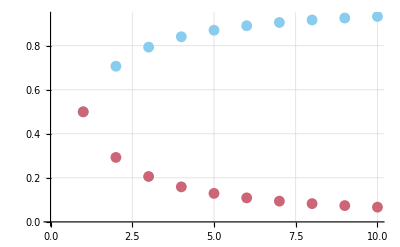

```mathematica
ListPlot[Evaluate@T@Table[{{n,2^(-1/n)},{n,1-2^(-1/n)}},{n,10}],GridLines->Auto]
```

```mathematica
{2^(-1/6),1-2^(-1/6)}//N
```

{0.890899,0.109101}

```mathematica
Solve[0.99^n==1/10,n]
```

{{n→229.105}}

```mathematica
(* error of maximum-likelihood *)
(13+1)/(13-1-6)//N
```

2.33333